```mathematica
|I|=6
```

```mathematica
|U|=12
```

```mathematica
U={1->5,2->5,3->1,3->4,3->5,4->1,4->2,4->6,5->4,6->2,6->3,6->5}
```

```mathematica
b={7,4,-1,-7,-2,-1}
```

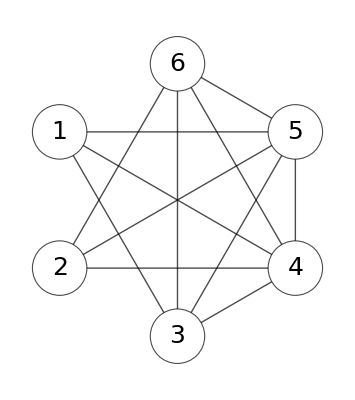

```mathematica
Исходный граф:
```

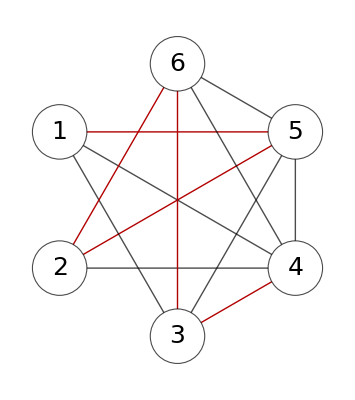

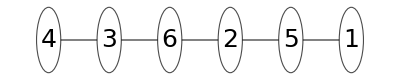

```mathematica
Граф с выделенным покрывающим деревом и 
соответствующее покрывающему дереву корневое дерево:
```

```mathematica
Списковые структуры корневого дерева:
```

```mathematica
Династический обход :{4,3,6,2,5,1}
```

Вершины | 1 | 2 | 3 | 4 | 5 | 6
Список предков | 5 | 6 | 4 | 0 | 2 | 3
Список глубин | 5 | 3 | 1 | 0 | 4 | 2
Список направлений | -1 | 1 | -1 | 0 | 1 | -1

```mathematica
Любое частное решение:
```

{(x̃)_(1,5)→7,(x̃)_(2,5)→-5,(x̃)_(3,1)→0,(x̃)_(3,4)→7,(x̃)_(3,5)→0,(x̃)_(4,1)→0,(x̃)_(4,2)→0,(x̃)_(4,6)→0,(x̃)_(5,4)→0,(x̃)_(6,2)→-9,(x̃)_(6,3)→8,(x̃)_(6,5)→0}

```mathematica
Табличная форма:
```

(x̃)_(1,5)→7
(x̃)_(2,5)→-5
(x̃)_(3,1)→0
(x̃)_(3,4)→7
(x̃)_(3,5)→0
(x̃)_(4,1)→0
(x̃)_(4,2)→0
(x̃)_(4,6)→0
(x̃)_(5,4)→0
(x̃)_(6,2)→-9
(x̃)_(6,3)→8
(x̃)_(6,5)→0

```mathematica
Проверка частного решения(Simplify):
```

{True,True,True,True,True,True}

```mathematica
Un = {2->5,3->1,3->5,4->1,4->6,5->4,6->2}
```

```mathematica
Ut = {4->2,3->4,6->3,6->5,1->5}
```

```mathematica
Характеристические вектора в ТФ:
```

| 3->1 | 3->5 | 4->1 | 4->2 | 4->6 | 5->4 | 6->5
3->1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
3->5 | 0 | 1 | 0 | 0 | 0 | 0 | 0
4->1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
4->2 | 0 | 0 | 0 | 1 | 0 | 0 | 0
4->6 | 0 | 0 | 0 | 0 | 1 | 0 | 0
5->4 | 0 | 0 | 0 | 0 | 0 | 1 | 0
6->5 | 0 | 0 | 0 | 0 | 0 | 0 | 1
3->4 | 0 | 0 | 1 | 1 | 1 | -1 | 0
6->3 | 1 | 1 | 1 | 1 | 1 | -1 | 0
6->2 | -1 | -1 | -1 | -1 | 0 | 1 | -1
2->5 | -1 | -1 | -1 | 0 | 0 | 1 | -1
1->5 | 1 | 0 | 1 | 0 | 0 | 0 | 0

```mathematica
deltas:
```

{δ_(3,1)^(3->1)→1,δ_(3,5)^(3->1)→0,δ_(4,1)^(3->1)→0,δ_(4,2)^(3->1)→0,δ_(4,6)^(3->1)→0,δ_(5,4)^(3->1)→0,δ_(6,5)^(3->1)→0,δ_(3,4)^(3->1)→0,δ_(6,3)^(3->1)→1,δ_(6,2)^(3->1)→-1,δ_(2,5)^(3->1)→-1,δ_(1,5)^(3->1)→1,δ_(3,1)^(3->5)→0,δ_(3,5)^(3->5)→1,δ_(4,1)^(3->5)→0,δ_(4,2)^(3->5)→0,δ_(4,6)^(3->5)→0,δ_(5,4)^(3->5)→0,δ_(6,5)^(3->5)→0,δ_(3,4)^(3->5)→0,δ_(6,3)^(3->5)→1,δ_(6,2)^(3->5)→-1,δ_(2,5)^(3->5)→-1,δ_(1,5)^(3->5)→0,δ_(3,1)^(4->1)→0,δ_(3,5)^(4->1)→0,δ_(4,1)^(4->1)→1,δ_(4,2)^(4->1)→0,δ_(4,6)^(4->1)→0,δ_(5,4)^(4->1)→0,δ_(6,5)^(4->1)→0,δ_(3,4)^(4->1)→1,δ_(6,3)^(4->1)→1,δ_(6,2)^(4->1)→-1,δ_(2,5)^(4->1)→-1,δ_(1,5)^(4->1)→1,δ_(3,1)^(4->2)→0,δ_(3,5)^(4->2)→0,δ_(4,1)^(4->2)→0,δ_(4,2)^(4->2)→1,δ_(4,6)^(4->2)→0,δ_(5,4)^(4->2)→0,δ_(6,5)^(4->2)→0,δ_(3,4)^(4->2)→1,δ_(6,3)^(4->2)→1,δ_(6,2)^(4->2)→-1,δ_(2,5)^(4->2)→0,δ_(1,5)^(4->2)→0,δ_(3,1)^(4->6)→0,δ_(3,5)^(4->6)→0,δ_(4,1)^(4->6)→0,δ_(4,2)^(4->6)→0,δ_(4,6)^(4->6)→1,δ_(5,4)^(4->6)→0,δ_(6,5)^(4->6)→0,δ_(3,4)^(4->6)→1,δ_(6,3)^(4->6)→1,δ_(6,2)^(4->6)→0,δ_(2,5)^(4->6)→0,δ_(1,5)^(4->6)→0,δ_(3,1)^(5->4)→0,δ_(3,5)^(5->4)→0,δ_(4,1)^(5->4)→0,δ_(4,2)^(5->4)→0,δ_(4,6)^(5->4)→0,δ_(5,4)^(5->4)→1,δ_(6,5)^(5->4)→0,δ_(3,4)^(5->4)→-1,δ_(6,3)^(5->4)→-1,δ_(6,2)^(5->4)→1,δ_(2,5)^(5->4)→1,δ_(1,5)^(5->4)→0,δ_(3,1)^(6->5)→0,δ_(3,5)^(6->5)→0,δ_(4,1)^(6->5)→0,δ_(4,2)^(6->5)→0,δ_(4,6)^(6->5)→0,δ_(5,4)^(6->5)→0,δ_(6,5)^(6->5)→1,δ_(3,4)^(6->5)→0,δ_(6,3)^(6->5)→0,δ_(6,2)^(6->5)→-1,δ_(2,5)^(6->5)→-1,δ_(1,5)^(6->5)→0}

```mathematica
Общее решение:
```

{x_(3,4)→7+x_(4,1)+x_(4,2)+x_(4,6)-x_(5,4),x_(6,3)→8+x_(3,1)+x_(3,5)+x_(4,1)+x_(4,2)+x_(4,6)-x_(5,4),x_(6,2)→-9-x_(3,1)-x_(3,5)-x_(4,1)-x_(4,2)+x_(5,4)-x_(6,5),x_(2,5)→-5-x_(3,1)-x_(3,5)-x_(4,1)+x_(5,4)-x_(6,5),x_(1,5)→7+x_(3,1)+x_(4,1)}

```mathematica
Табличная форма:
```

x_(3,4)→7+x_(4,1)+x_(4,2)+x_(4,6)-x_(5,4)
x_(6,3)→8+x_(3,1)+x_(3,5)+x_(4,1)+x_(4,2)+x_(4,6)-x_(5,4)
x_(6,2)→-9-x_(3,1)-x_(3,5)-x_(4,1)-x_(4,2)+x_(5,4)-x_(6,5)
x_(2,5)→-5-x_(3,1)-x_(3,5)-x_(4,1)+x_(5,4)-x_(6,5)
x_(1,5)→7+x_(3,1)+x_(4,1)

```mathematica
Проверка общего решения(Simplify):
```

{True,True,True,True,True,True}